```mathematica
(*eta = 0.5, 1.5, 3*)
(*Rm ~ 1, 3, 10*)
```

```mathematica
a=Specz[0.5,0.1,0.1,3,3]
Round[Re[ev]/0.1-a[[1]],10.^-5]
```

{10.2035,19.8645,19.8645,7,7,9,0.1,{101.085,90.3044,80.1057,60.2382,50.0407,40.2657,30.068,10.2035},0.0489138}

{90.8813,80.1009,69.9021,50.0347,39.8372,30.0622,19.8645,0.,-10.2104,-10.2048,-10.2042,-10.2037,-10.2036,-10.2035,-10.2035,-10.2035}

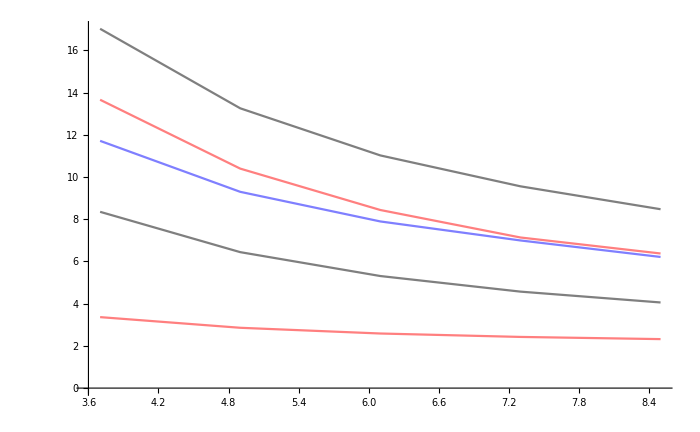

```mathematica
ListPlot[Transpose[Table[Tuples[{{(0.25+0.12k)/0.1},Specz[3.,0.1,0.25+0.12k,6,6][[8]][[-5;;-1]]}],{k,1,5}]],Joined->True,PlotStyle->{{Black, Opacity[0.5]},{Red, Opacity[0.5]},{Blue, Opacity[0.5]}},PlotRange->Automatic]
```

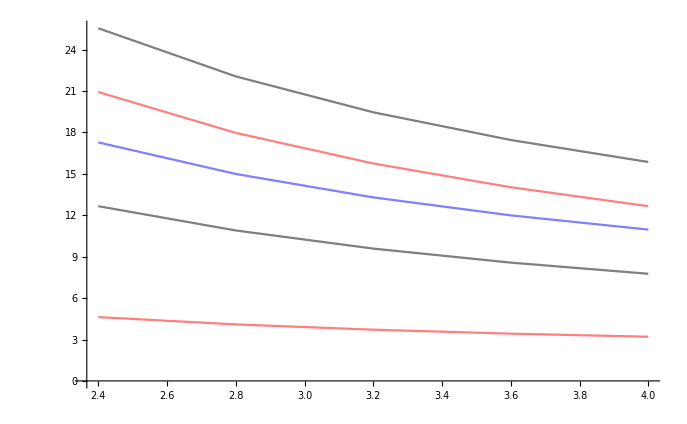

```mathematica
ListPlot[Transpose[Table[Tuples[{{(0.2+0.04k)/0.1},Specz[1.5,0.1,0.2+0.04k,6,6][[8]][[-5;;-1]]}],{k,1,5}]],Joined->True,PlotStyle->{{Black, Opacity[0.5]},{Red, Opacity[0.5]},{Blue, Opacity[0.5]}},PlotRange->Automatic]
```

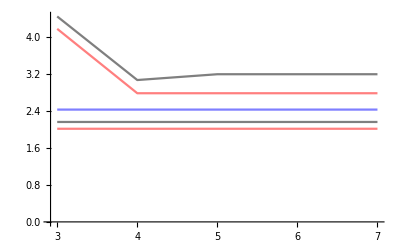

```mathematica
ListPlot[Transpose[Table[Tuples[{{3+k},Specz[1.5,0.1,3.6,3+k,3+k][[8]][[-5;;-1]]}],{k,0,4}]],Joined->True,PlotStyle->{{Black, Opacity[0.5]},{Red, Opacity[0.5]},{Blue, Opacity[0.5]}},PlotRange->Automatic]
```

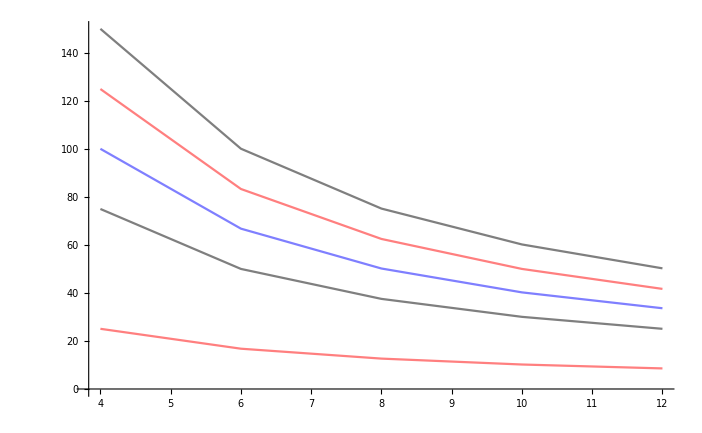

```mathematica
ListPlot[Transpose[Table[Tuples[{{(0.02+0.02k)/0.01},Specz[0.5,0.1,0.02+0.02k,6,6][[8]][[-5;;-1]]}],{k,1,5}]],Joined->True,PlotStyle->{{Black, Opacity[0.5]},{Red, Opacity[0.5]},{Blue, Opacity[0.5]}},PlotRange->Automatic]
```

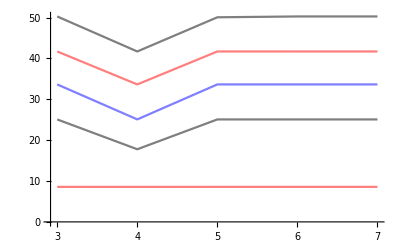

```mathematica
ListPlot[Transpose[Table[Tuples[{{3+k},Specz[0.5,0.1,0.12,3+k,3+k][[8]][[-5;;-1]]}],{k,0,4}]],Joined->True,PlotStyle->{{Black, Opacity[0.5]},{Red, Opacity[0.5]},{Blue, Opacity[0.5]}},PlotRange->Automatic]
```

```mathematica
Spec[eta_,m_,scale_]:={h=(m/eta)^(15/8);R=scale/m;M=Floor[Sqrt[R/16]];rs=RS[M];ns=NSS[M];A=Table[Join[Table[If[iq==ip,H0[ns[[iq]],R,m],0],{ip,Length[ns]}],Table[Conjugate[dH[ns[[iq]],rs[[jp]],R,m]],{jp,Length[rs]}]],{iq,Length[ns]}];
B=Table[Join[Table[dH[ns[[ip]],rs[[jq]],R,m],{ip,Length[ns]}],Table[If[j==jp,H0[rs[[jq]],R,m],0],{jp,Length[rs]}]],{jq,Length[rs]}];
H=Join[A,B];ee=Eigensystem[H];
ev=ee[[1]];
vec=ee[[2]];gsi=Length[Select[Re[ev]/m,#>10.^-3&]];gse=Round[Re[ev[[gsi]]/m],10.^-5];
exe=Round[Re[ev[[gsi-1]]/m],10.^-5];
ssi=Length[Select[Re[ev]/m,#>gse+0.5&]];
sse=Round[Re[ev[[ssi]]/m],10.^-5];
(*gs=Round[vec[[gsi]],10.^-2];*)
{gse,exe-gse,sse-gse,ssi,Length[ns],Length[rs],R Abs[h]^(8/15),Round[Re[ev]/m,10.^-5],R,1/m,h}}[[1]]
```

```mathematica
Specv[eta_,m_,scale_]:={h=(m/eta)^(15/8);R=scale/m;M=Floor[Sqrt[R/16]];rs=RS[M];ns=NSS[M];A=Table[Join[Table[If[iq==ip,H0[ns[[iq]],R,m],0],{ip,Length[ns]}],Table[Conjugate[dH[ns[[iq]],rs[[jp]],R,m]],{jp,Length[rs]}]],{iq,Length[ns]}];
B=Table[Join[Table[dH[ns[[ip]],rs[[jq]],R,m],{ip,Length[ns]}],Table[If[j==jp,H0[rs[[jq]],R,m],0],{jp,Length[rs]}]],{jq,Length[rs]}];
H=Join[A,B];ee=Eigensystem[H];
ev=ee[[1]];
vec=ee[[2]];gsi=Length[Select[Re[ev]/m,#>10.^-3&]];gse=Round[Re[ev[[gsi]]/m],10.^-5];
exe=Round[Re[ev[[gsi-1]]/m],10.^-5];
ssi=Length[Select[Re[ev]/m,#>gse+0.5&]];
sse=Round[Re[ev[[ssi]]/m],10.^-5];
(*gs=Round[vec[[gsi]],10.^-2];*)
{gse,exe-gse,sse-gse,ssi,Length[ns],Length[rs],R}}[[1]]
```

```mathematica
Specz[eta_,m_,scale_,min_,max_]:={h=(m/eta)^(15/8);R=scale/m;M=Floor[Sqrt[R/16]];rs=RS[Min[Max[M,min],max]];ns=NSS[Min[Max[M,min],max]];A=Table[Join[Table[If[iq==ip,H0[ns[[iq]],R,m],0],{ip,Length[ns]}],Table[Conjugate[h*dH[ns[[iq]],rs[[jp]],R,m]],{jp,Length[rs]}]],{iq,Length[ns]}];
B=Table[Join[Table[h*dH[ns[[ip]],rs[[jq]],R,m],{ip,Length[ns]}],Table[If[j==jp,H0[rs[[jq]],R,m],0],{jp,Length[rs]}]],{jq,Length[rs]}];
H=Join[A,B];ee=Eigensystem[H];
ev=ee[[1]];
vec=ee[[2]];gsi=Length[Select[Re[ev]/m,Abs[#]>10.^-1&]];gse=Round[Re[ev[[gsi]]/m],10.^-5];
exe=Round[Re[ev[[gsi-1]]/m],10.^-5];
ssi=Length[Select[Re[ev]/m,#>gse+0.5&]];
sse=Round[Re[ev[[ssi]]/m],10.^-5];
(*gs=Round[vec[[gsi]],10.^-2];*)
{gse,exe-gse,sse-gse,ssi,Length[ns],Length[rs],R m,Round[Re[ev]/m,10.^-5][[1;;gsi]],h}}[[1]]
```

```mathematica
NSS[M_]:=Select[Subsets[Reap[For[i=-M,i<M,i++,Sow[i+1/2]]][[-1]][[-1]],{2,2M,2}],Total[#]==0&]
RS[M_]:=Select[Subsets[Reap[For[i=-M,i<=M,i++,Sow[i]]][[-1]][[-1]],{1,2M,2}],Total[#]==0&]
```

```mathematica
dH[nss_,rss_,R_,m_]:={l=Length[nss];n=Length[rss];S=(-1)^(l(l-1)/2)m^(1/8)(2I)^((l+n-1)/2);For[i=1,i≤l,i++,S*=1/√(4π Sqrt[m^2 R^2+nss[[i]]^2]);For[j=1,j<i,j++,S*=(nss[[j]]-nss[[i]])/(√(m^2 R^2+nss[[i]]^2)+√(m^2 R^2+nss[[j]]^2))]];For[i=1,i≤n,i++,S*=1/√(4π Sqrt[m^2 R^2+rss[[i]]^2]);For[j=1,j<i,j++,S*=(rss[[j]]-rss[[i]])/(√(m^2 R^2+rss[[i]]^2)+√(m^2 R^2+rss[[j]]^2))];For[j=1,j≤l,j++,S*=(√(m^2 R^2+rss[[i]]^2)+√(m^2 R^2+nss[[j]]^2))/(nss[[j]]-rss[[i]])]]; S}[[1]]
H0[s_,R_,m_]:={S=0;For[i=1,i≤Length[s],i++,S+=√(m^2+s[[i]]^2/R^2);];S}[[1]]
```